```mathematica
P[u_]=(21 - 3 u + 3 u^2 - u^3) / 20
```

1/20 (21-3 u+3 u^2-u^3)

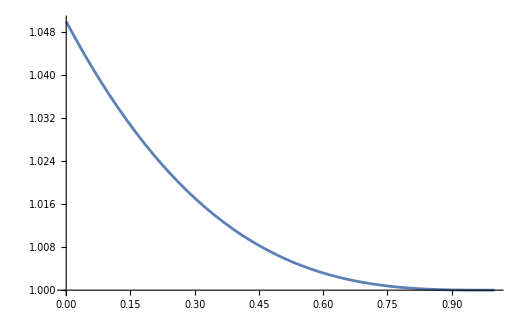

```mathematica
Plot[P[u],{u,0,1}]
```

```mathematica
(** P[u] is the marginal price we pay, if the book is filled with u = min[1,q/Q] **)
```

```mathematica
(** Now suppose we go from q < Q, to q - dq < q < Q, the amount paid is given by **)
```

```mathematica
paid[dq_]=FullSimplify[Q Integrate[P[u],{u,(q-dq)/Q,q/Q}]]
```

(dq (dq^3+6 dq (q-Q)^2+4 dq^2 (-q+Q)-4 (q^3-3 q^2 Q+3 q Q^2-21 Q^3)))/(80 Q^3)

```mathematica
(** And the newton update is **)
```

```mathematica
frac=FullSimplify[y-(paid[y]-x)/D[paid[y],y]]
```

-(80 Q^3 x+6 (q-Q)^2 y^2+8 (-q+Q) y^3+3 y^4)/(4 (q^3-21 Q^3-3 Q^2 y-3 Q y^2-y^3-3 q^2 (Q+y)+3 q (Q+y)^2))

```mathematica
num=-Numerator[frac]
```

80 Q^3 x+6 (q-Q)^2 y^2+8 (-q+Q) y^3+3 y^4

```mathematica
den=FullSimplify[-Denominator[frac]/.y->z+q]/.z->y-q
```

4 (21 Q^3+3 Q^2 (-q+y)+3 Q (-q+y)^2+(-q+y)^3)

```mathematica
step[y_]=num/den
```

(80 Q^3 x+6 (q-Q)^2 y^2+8 (-q+Q) y^3+3 y^4)/(4 (21 Q^3+3 Q^2 (-q+y)+3 Q (-q+y)^2+(-q+y)^3))

```mathematica
x-paid[step[step[step[x]]]](1-10^(-9))/.{Q->1,q->0.5,x->0.2}
```

2.×10^-10